## Panare 2DoF (RR):

```mathematica
Planare2dofIK[x_,y_]:=Module[{L1,L2,hx,hy,hh,q1,q2,JJ,p,ll,F,eq,eeq,tf,hhx,hhy,t},
(*Verifico parametri*)
If[ListQ[x]!=False,Print["The argument 1 must be a scalar" ];Return[Null]];
If[ListQ[y]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];

L1=1;
L2=1;

hx=L1*Cos[q1]+L2*Cos[q1+q2];
hy=L1*Sin[q1]+L2*Sin[q1+q2];

JJ={{D[hx,q1],D[hx,q2]},
{D[hy,q1],D[hy,q2]}};

hh={{hx},{hy}};

p={{x},{y}} ;

ll=1;

F=Simplify[ll*Inverse[JJ].(p-hh)];

eq={{q1'[t]},{q2'[t]}}-(F /. {q1->q1[t],q2->q2[t]});
eeq=Flatten[eq];

tf=1;

sol=NDSolve[{eeq[[1]]==0,eeq[[2]]==0,q1[0]==1,q2[0]==1},{q1[t],q2[t]},{t,0,tf}];


hhx[t]=hx/.{q1->q1[t],q2->q2[t]};
hhy[t]=hy/.{q1->q1[t],q2->q2[t]};

{Plot[Evaluate[{hhx[t],hhy[t]}/. sol ],{t,0,tf},PlotRange->All],Plot[Evaluate[{q1[t],q2[t]}/. sol ],{t,0,tf},PlotRange->All]}
]
```

### test:

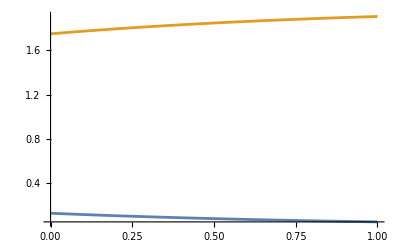
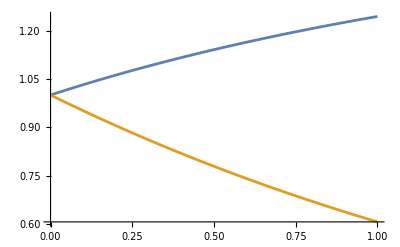

```mathematica
Planare2dofIK[0,2]
```

## Cartesiano 3DoF (PPP):

```mathematica
Cartesiano3dofIK[x_,y_,z_]:=Module[{hx,hy,hz,hh,q1,q2,q3,JJ,p,ll,F,eq,eeq,tf,hhx,hhy,hhz,t},
(*Verifico parametri*)
If[ListQ[x]!=False,Print["The argument 1 must be a scalar" ];Return[Null]];
If[ListQ[y]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];
If[ListQ[y]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];

hx=q1;
hy=q2;
hz=q3;

JJ={{D[hx,q1],D[hx,q2], D[hx,q3]},
{D[hy,q1],D[hy,q2], D[hy,q3]},
{D[hz,q1],D[hz,q2], D[hz,q3]}} ;

hh={{hx},{hy},{hz}};

p={{x},{y},{z}} ;

ll=1;

F=Simplify[ll*Inverse[JJ].(p-hh)];

eq={{q1'[t]},{q2'[t]},{q3'[t]}}-(F /. {q1->q1[t],q2->q2[t],q3->q3[t]});
eeq=Flatten[eq];

tf=10;

sol=NDSolve[{eeq[[1]]==0,eeq[[2]]==0,eeq[[3]]==0,q1[0]==0,q2[0]==0,q3[0]==0},{q1[t],q2[t],q3[t]},{t,0,tf}];


hhx[t]=hx/.{q1->q1[t],q2->q2[t],q3->q3[t]};
hhy[t]=hy/.{q1->q1[t],q2->q2[t],q3->q3[t]};
hhz[t]=hz/.{q1->q1[t],q2->q2[t],q3->q3[t]};

{Plot[Evaluate[{hhx[t],hhy[t],hhz[t]}/. sol ],{t,0,tf},PlotRange->All],Plot[Evaluate[{q1[t],q2[t],q3[t]}/. sol ],{t,0,tf},PlotRange->All]}
]
```

### test:

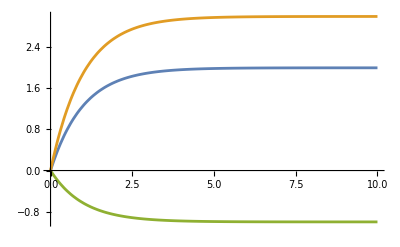
{-Graphics-,-Graphics-}

```mathematica
Cartesiano3dofIK[2,3,-1]
```

## Cilindrico 3DoF (RPP):

```mathematica
Cilindrico3dofIK[x_,y_,z_]:=Module[{D1,hx,hy,hz,hh,q1,q2,q3,JJ,p,ll,F,eq,eeq,tf,hhx,hhy,hhz,t},
(*Verifico parametri*)
If[ListQ[x]!=False,Print["The argument 1 must be a scalar" ];Return[Null]];
If[ListQ[y]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];
If[ListQ[y]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];

D1=1;

hx=-q3*Sin[q1];
hy=q3*Cos[q1];
hz=D1+q2;

JJ={{D[hx,q1],D[hx,q2], D[hx,q3]},
{D[hy,q1],D[hy,q2], D[hy,q3]},
{D[hz,q1],D[hz,q2], D[hz,q3]}} ;

hh={{hx},{hy},{hz}};

p={{x},{y},{z}} ;

ll=1;

F=Simplify[ll*Transpose[JJ].(p-hh)];(* qui Trasposta perche sempre singolare *)

eq={{q1'[t]},{q2'[t]},{q3'[t]}}-(F /. {q1->q1[t],q2->q2[t],q3->q3[t]});
eeq=Flatten[eq];

tf=10;

sol=NDSolve[{eeq[[1]]==0,eeq[[2]]==0,eeq[[3]]==0,q1[0]==1,q2[0]==1,q3[0]==1},{q1[t],q2[t],q3[t]},{t,0,tf}];


hhx[t]=hx/.{q1->q1[t],q2->q2[t],q3->q3[t]};
hhy[t]=hy/.{q1->q1[t],q2->q2[t],q3->q3[t]};
hhz[t]=hz/.{q1->q1[t],q2->q2[t],q3->q3[t]};

{Plot[Evaluate[{hhx[t],hhy[t],hhz[t]}/. sol ],{t,0,tf},PlotRange->All],Plot[Evaluate[{q1[t],q2[t],q3[t]}/. sol ],{t,0,tf},PlotRange->All]}
]
```

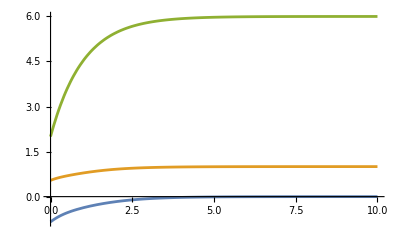
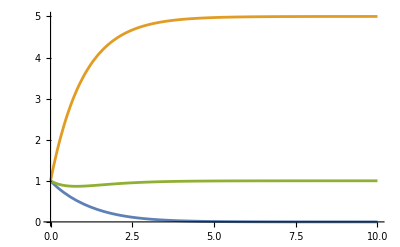

```mathematica
Cilindrico3dofIK[0,1,6]
```

## Scara 3 DoF (RRP):

```mathematica
Scara3dofIK[x_,y_,z_]:=Module[{L1,L2,D1,D2,hx,hy,hz,hh,q1,q2,q3,JJ,p,ll,F,eq,eeq,tf,hhx,hhy,hhz,t},
(*Verifico parametri*)
If[ListQ[x]!=False,Print["The argument 1 must be a scalar" ];Return[Null]];
If[ListQ[y]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];
If[ListQ[y]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];

D1=1;
D2=1;
L1=1;
L2=1;

hx=L1*Cos[q1]+L2*Cos[q1+q2];
hy=L1*Sin[q1]+L2*Sin[q1+q2];
hz=D1+D2+q3;

JJ={{D[hx,q1],D[hx,q2], D[hx,q3]},
{D[hy,q1],D[hy,q2], D[hy,q3]},
{D[hz,q1],D[hz,q2], D[hz,q3]}} ;

hh={{hx},{hy},{hz}};

p={{x},{y},{z}} ;

ll=1;

F=Simplify[ll*Transpose[JJ].(p-hh)];(* qui Trasposta perche sempre singolare *)

eq={{q1'[t]},{q2'[t]},{q3'[t]}}-(F /. {q1->q1[t],q2->q2[t],q3->q3[t]});
eeq=Flatten[eq];

tf=10;

sol=NDSolve[{eeq[[1]]==0,eeq[[2]]==0,eeq[[3]]==0,q1[0]==1,q2[0]==1,q3[0]==1},{q1[t],q2[t],q3[t]},{t,0,tf}];


hhx[t]=hx/.{q1->q1[t],q2->q2[t],q3->q3[t]};
hhy[t]=hy/.{q1->q1[t],q2->q2[t],q3->q3[t]};
hhz[t]=hz/.{q1->q1[t],q2->q2[t],q3->q3[t]};

{Plot[Evaluate[{hhx[t],hhy[t],hhz[t]}/. sol ],{t,0,tf},PlotRange->All],Plot[Evaluate[{q1[t],q2[t],q3[t]}/. sol ],{t,0,tf},PlotRange->All]}
]
```

### test:

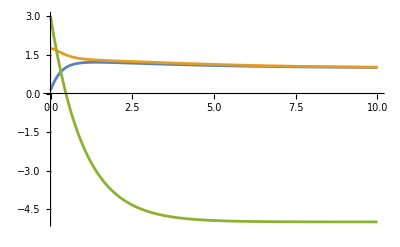
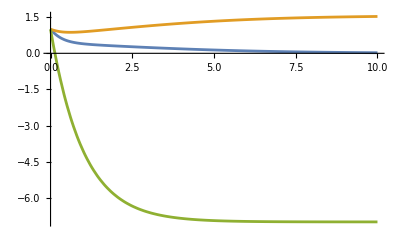

```mathematica
Scara3dofIK[1,1,-5]
```

## Sferico di 1° tipo 3 DoF (RRP):

```mathematica
Sferico1Tipo3dofIK[x_,y_,z_]:=Module[{L2,D1,hx,hy,hz,hh,q1,q2,q3,JJ,p,ll,F,eq,eeq,tf,hhx,hhy,hhz,t},
(*Verifico parametri*)
If[ListQ[x]!=False,Print["The argument 1 must be a scalar" ];Return[Null]];
If[ListQ[y]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];
If[ListQ[y]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];

D1=1;
L2=1;

hx=(L2*Cos[q2]+q3*Sin[q2])*Cos[q1];
hy=(L2*Cos[q2]+q3*Sin[q2])*Sin[q1];
hz=L2*Sin[q2]-q3*Cos[q2]+D1;

JJ={{D[hx,q1],D[hx,q2], D[hx,q3]},
{D[hy,q1],D[hy,q2], D[hy,q3]},
{D[hz,q1],D[hz,q2], D[hz,q3]}} ;

hh={{hx},{hy},{hz}};

p={{x},{y},{z}} ;

ll=1;

F=Simplify[ll*Transpose[JJ].(p-hh)];(* qui Trasposta perche sempre singolare *)

eq={{q1'[t]},{q2'[t]},{q3'[t]}}-(F /. {q1->q1[t],q2->q2[t],q3->q3[t]});
eeq=Flatten[eq];

tf=10;

sol=NDSolve[{eeq[[1]]==0,eeq[[2]]==0,eeq[[3]]==0,q1[0]==1,q2[0]==1,q3[0]==1},{q1[t],q2[t],q3[t]},{t,0,tf}];


hhx[t]=hx/.{q1->q1[t],q2->q2[t],q3->q3[t]};
hhy[t]=hy/.{q1->q1[t],q2->q2[t],q3->q3[t]};
hhz[t]=hz/.{q1->q1[t],q2->q2[t],q3->q3[t]};

{Plot[Evaluate[{hhx[t],hhy[t],hhz[t]}/. sol ],{t,0,tf},PlotRange->All],Plot[Evaluate[{q1[t],q2[t],q3[t]}/. sol ],{t,0,tf},PlotRange->All]}
]
```

### test:

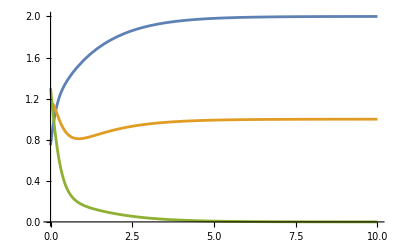
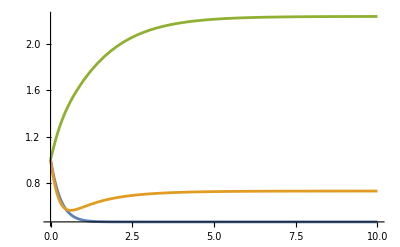

```mathematica
Sferico1Tipo3dofIK[2,1,0]
```

## Sferico Standford 3 DoF (RRP):

```mathematica
SfericoStandford3dofIK[x_,y_,z_]:=Module[{D1,D2,hx,hy,hz,hh,q1,q2,q3,JJ,p,ll,F,eq,eeq,tf,hhx,hhy,hhz,t},
(*Verifico parametri*)
If[ListQ[x]!=False,Print["The argument 1 must be a scalar" ];Return[Null]];
If[ListQ[y]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];
If[ListQ[y]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];

D1=1;
D2=1;

hx=q3*Cos[q1]*Sin[q2]-D2*Sin[q1];
hy=q3*Sin[q1]*Sin[q2]+D2*Cos[q1];
hz=q3*Cos[q2]+D1;

JJ={{D[hx,q1],D[hx,q2], D[hx,q3]},
{D[hy,q1],D[hy,q2], D[hy,q3]},
{D[hz,q1],D[hz,q2], D[hz,q3]}} ;

hh={{hx},{hy},{hz}};

p={{x},{y},{z}} ;

ll=1;

F=Simplify[ll*Transpose[JJ].(p-hh)];(* qui Trasposta perche sempre singolare *)

eq={{q1'[t]},{q2'[t]},{q3'[t]}}-(F /. {q1->q1[t],q2->q2[t],q3->q3[t]});
eeq=Flatten[eq];

tf=10;

sol=NDSolve[{eeq[[1]]==0,eeq[[2]]==0,eeq[[3]]==0,q1[0]==1,q2[0]==1,q3[0]==1},{q1[t],q2[t],q3[t]},{t,0,tf}];


hhx[t]=hx/.{q1->q1[t],q2->q2[t],q3->q3[t]};
hhy[t]=hy/.{q1->q1[t],q2->q2[t],q3->q3[t]};
hhz[t]=hz/.{q1->q1[t],q2->q2[t],q3->q3[t]};

{Plot[Evaluate[{hhx[t],hhy[t],hhz[t]}/. sol ],{t,0,tf},PlotRange->All],Plot[Evaluate[{q1[t],q2[t],q3[t]}/. sol ],{t,0,tf},PlotRange->All]}
]
```

### test:

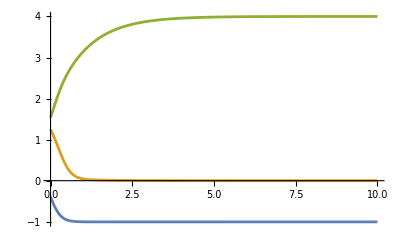
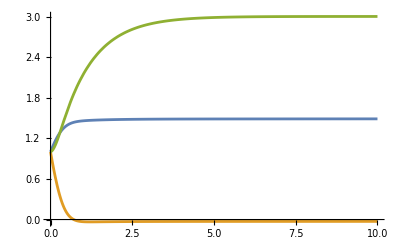

```mathematica
SfericoStandford3dofIK[-1,0,4]
```